35000.5

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

| Estimate | Standard Error | t-Statistic | P-Value
a | 4.37975 | 0.114696 | 38.1855 | 1.1764×10^-38

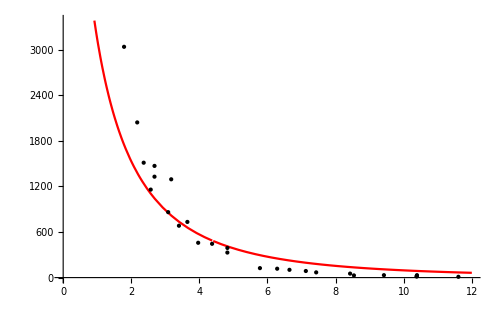

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["datos2_ready_parsec.dat"];
L=Length[data];
alpha=35000.5(*Fijando alpha para que se pueda hacer el ajuste*)
Ip[R_]:=Piecewise[{{alpha*((2+(R/a)^2)*(Log[(1+Sqrt[1-(R/a)^2])/(R/a)]/(Sqrt[1-(R/a)^2]))-3)/(a^2*(1-(R/a)^2)^2),R<a},{2*alpha/(7.5*a*a),R==a},{alpha*((2+(R/a)^2)*(ArcCos[1/(R/a)]/Sqrt[(R/a)^2-1])-3)/(a^2*(1-(R/a)^2)^2),R>a}}];
(*Plot[Ip[R],{R,0,4}]*)
fit = NonlinearModelFit[data,Ip[R],{a},R,MaxIterations->1000];
(*fit["BestFit"]*)
fit["ParameterTable"]
Plot[fit[R],{R,0,12},PlotStyle->Red,Epilog:>Point[data],ImageSize->500]
```